```mathematica
Quit[]
```

# MeV-DM: Scalar Mediator model

Load `HazmaTools`.Note that this will load `FeynCalc` and the patched `FeynArts`

```mathematica
<<HazmaTools`
$HazmaModel="scalar";
```

FeynCalc::tfadvice: You are not using TraditionalForm as the default format type of new output cells. Without TraditionalForm FeynCalc cannot use built-in typeseting rules that make various objects like Lorentz vectors or Dirac matrices look nicer. To change the format type go to Edit->Preferences->Evaluation.

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

args::shdw: Symbol args appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

MeV-DM - Scalar Mediator: version 0.2.1

by Adam Coogan and Logan A. Morrison

Gluon::shdw: Symbol Gluon appears in multiple contexts {HazmaTools`,Global`}; definitions in context HazmaTools` may shadow or be shadowed by other definitions.

## Utilities

AP approximations for spectra. See arXiv:hep-ph/0507194.

```mathematica
dndxAPFermion=alphaEM/π((1+(1-x)^2)/x)(Log[(1-x)/μl^2]-1);
dndxAPScalar=alphaEM/π((1-x)/x)(Log[(1-x)/μπ^2]-1);
```

## Amplitudes

```mathematica
(* x + xbar-> l + lbar *)
amplitudeLL=HazmaComputeAmplitude[{DarkMatter,AntiDarkMatter},{Lepton,AntiLepton},IncomingMomenta->{px,pxbar},OutgoingMomenta->{pl,plbar}];
(* x + xbar-> gamma + gamma *)
amplitudeGG=HazmaComputeAmplitude[{DarkMatter,AntiDarkMatter},{Photon,Photon}];
(* x + xbar-> pi0 + pi0 *)
amplitudeπ0π0=HazmaComputeAmplitude[{DarkMatter,AntiDarkMatter},{NeutralPion,NeutralPion}];
(* x + xbar-> pi + pi *)
amplitudeπpπm=HazmaComputeAmplitude[{DarkMatter,AntiDarkMatter},{ChargedPionM,ChargedPionP}];
(* x + xbar-> S + S *)
amplitudeSS=HazmaComputeAmplitude[{DarkMatter,AntiDarkMatter},{ScalarMediator,ScalarMediator}];
```

## Squared Amplitudes

```mathematica
(* x + xbar-> l + lbar *)
msqrdLL=HazmaComputeAmplitudeSquared[{DarkMatter,AntiDarkMatter},{Lepton,AntiLepton},IncomingMomenta->{px,pxbar},OutgoingMomenta->{pl,plbar}];
(* x + xbar-> gamma + gamma *)
msqrdGG=HazmaComputeAmplitudeSquared[{DarkMatter,AntiDarkMatter},{Photon,Photon}];
(* x + xbar-> pi0 + pi0 *)
msqrdπ0π0=HazmaComputeAmplitudeSquared[{DarkMatter,AntiDarkMatter},{NeutralPion,NeutralPion}];
(* x + xbar-> pi + pi *)
msqrdπpπm=HazmaComputeAmplitudeSquared[{DarkMatter,AntiDarkMatter},{ChargedPionM,ChargedPionP}];
(* x + xbar-> S + S *)
msqrdSS=HazmaComputeAmplitudeSquared[{DarkMatter,AntiDarkMatter},{ScalarMediator,ScalarMediator}];
```

## Cross Sections

To Compute cross sections for 2->2 interactions, use: `HazmaComputeCrossSection22[inStates,outStates, ECM]`, where `inStates` and `outStates` are arrays of particles states and `ECM` is the variable for the center of mass energy.

```mathematica
(* x + xbar-> l + lbar *)
crossSectionLL=HazmaComputeCrossSection22[{DarkMatter,AntiDarkMatter},{Lepton,AntiLepton},Q];
(* x + xbar-> gamma + gamma *)
crossSectionGG=HazmaComputeCrossSection22[{DarkMatter,AntiDarkMatter},{Photon,Photon},Q];
(* x + xbar-> pi0 + pi0 *)
crossSectionπ0π0=HazmaComputeCrossSection22[{DarkMatter,AntiDarkMatter},{NeutralPion,NeutralPion},Q];
(* x + xbar-> pi + pi *)
crossSectionπpπm=HazmaComputeCrossSection22[{DarkMatter,AntiDarkMatter},{ChargedPionM,ChargedPionP},Q];
(* x + xbar-> S + S *)
crossSectionSS=HazmaComputeCrossSection22[{DarkMatter,AntiDarkMatter},{ScalarMediator,ScalarMediator},Q];
```

## FSR Spectra

NOTE: You do not need to specify the photon in the `outStates`.

### χ̄ χ→ ℓ̄ ℓγ

```mathematica
dndeLL=HazmaComputeDNDE[{Lepton,AntiLepton}];
```

```mathematica
dndxLL=Q/2 ReplaceAll[dndeLL,{ms->Q,ml->Q*μl,Eγ->Q*x/2}]//Simplify[#,Assumptions->{Q>0,1-4 μl^2>x>0}]&;
```

Compare to AP approximation

```mathematica
Series[dndxLL,{μl,0,0},Assumptions->{Q>0,1>x>0,1/2>μl>0}];
dndxLLLimit=FullSimplify[%,Assumptions->{Q>0,1>x>0,1/2>μl>0}]//Normal;
```

The -1 and x terms just don’t matter in the μ << 1 limit.

```mathematica
dndxLLLimit=dndxAPFermion+(alphaEM x)/π;
```

### χ̄ χ→ π^+π^-γ

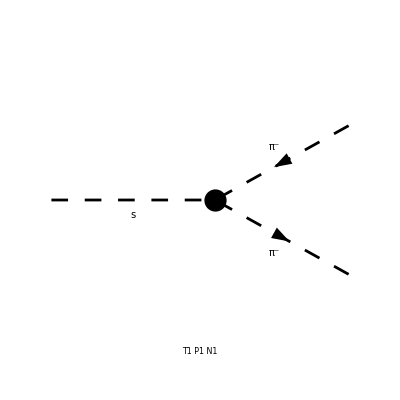

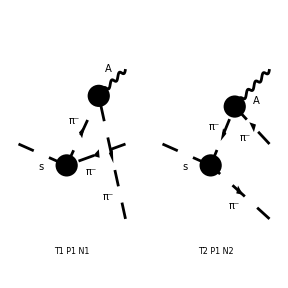

```mathematica
dndeππ=HazmaComputeDNDE[{ChargedPionP,ChargedPionM},Paint->True,Adjacencies->{3},FinalSubstitutions->{Join[ReplaceAll[M$FACouplings,{gsGG->0,vs->0}],{gsGG->0,vs->0}]}];
```

```mathematica
dndxππ=Q/2 ReplaceAll[dndeππ,{ms->Q,mpi->Q*μπ,Eγ->Q*x/2}]//Simplify[#,Assumptions->{Q>0,1-4 μπ^2>x>0}]&;
```

```mathematica
Series[dndxππ,{μπ,0,0},Assumptions->{Q>0,1>x>0,1/2>μπ>0}];
dndxππLimit=FullSimplify[%,Assumptions->{Q>0,1>x>0,1/2>μπ>0}]//Normal;
```

```mathematica
dndxππLimit
```

-(2 alphaEM (-1+x) (-1+Log[1-x]-2 Log[μπ]))/(π x)

Simplified by hand. TODO: why is this exactly a factor of two too large?

```mathematica
dndxππLimit=2dndxAPScalar;
```

### χ̄ χ→ π^+π^-γ with contact diagram removed

TODO: get this to run and check that it reduces to the AP expression! If it does, then we can conclude the factor of two difference above comes from the contact diagram.

```mathematica
dndeππ=HazmaComputeDNDE[{ChargedPionP,ChargedPionM},Adjacencies->{3}];
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.